### (*PARAMETER SETS FOR BROWN DWARF *) Parameters:

```mathematica
Vm=((220.*10^5)/c);
c=3*10^10;
Vd=Vm*√(3./2);
V0= √(8./(3*Pi))*Vd;
ρ0 =0.00854*38.16;
ρburkert =0.08931*38.16; rb= 7.7*(3.086*10^21);
rs= 19.6*(3.086*10^21);r= 8.14*(3.086*10^21); 
G= 6.67*10^-5/(5.61*10^26);Mn = 0.94; 
gamma=1; Mj= (1*1.98*10^27*5.61*10^26);
Rj= 69911.*10^5;dj=7.785472*(10^13);Tj=1.5*10^4*8.62*10^-14;ρj=2*10^4 * 5.61*10^26*10^-6;tj=1.5*10^17;tJG=0.3;
Vescscale =( √((2.*(6.67*10^-5)*(0.0378*1.989*10^30))/(69911*10^5)));Vescscale1 =( √((2.*(GN)*(10*1.989*10^27))/(69911*10^5)));
Mbj=1./1047;
mMED = 0.511; 
Nint = 7.53211274044683*10^-10; 
L= 5*10^18; 
sigmav = 5.1*10^-27;sigmav1 = 5.1*10^-32;sigmachi=10^-38;
ρcore = 500*(0.032/0.05)^2* 5.61*10^23;
Tcore = 2*10^5 * (0.032/0.05)^(4/3)*8.62*10^-14;
GN = 1.069*10^-39;
tage =10*10^9;
αe = 2.32;
μe=1.143;
γe= 0.6;Mbsun = 0.032;γe1=0.02;
ρ= ρ0/((r/rs)^gamma(1+(r/rs))^(3-gamma));
ρ1= (ρ0/((r/rs)^gamma(1+(r/rs))^(3-gamma)))/38.14;Const = (3/GN)^(3/2)*((10^5*8.62*10^-14)/(10*100*5.61*10^23))^(3/2);
```

```mathematica
teq1[1,1*10^-38,Mb,Rb,db,Mbj,tj];
```

1.66861×10^12

```mathematica
Tequi = ta^(3/4)*pa^(-3/4);
```

```mathematica
ta = 1.;pa=1000.;Tequi
```

0.00562341

```mathematica
Teqi is increasing with ta;Teqi is decreasing with pa
```

```mathematica
Vscal[mDM_?NumericQ,Mbs_?NumericQ,ta_?NumericQ] :=Const*(Tcal1[Mbs,ta]/1*10^5)^(3/2) (10/mDM)^(3/2)(100/ρcal1[Mbs,ta])^(3/2)
```

## Source Details:

### Source1:T6

```mathematica
Mb1= (34*1.898*10^27*5.61*10^26);
Mbs1=34./1047;
Rb1 = 0.97*69911.*10^5;
Nn1 = Mb1/Mn;
d1= 10.68*(3.086*10^18);
E1=1.09406*10^-9; 
E1n=1.8879227*10^-9; 
ta1 = 1.7*10^9*3.156*10^7;
Tc1= 3.35*10^5 ; 
ρc1 = 248.94;
```

### Source2:T8.5

```mathematica
Mb2= (26*1.898*10^27*5.61*10^26);
Mbs2=26./1047;
Rb2 = 0.88*69911.*10^5;
Nn2 = Mb2/Mn;
d2= 6.54*(3.086*10^18);
E2=1.62165*10^-9; 
E2n=1.5074990*10^-9; 
ta2 = 10*10^9*3.156*10^7;
Tc2= 1.40*10^5 ; 
ρc2 = 145.57;
```

### Source3:T1

```mathematica
Mb3= (47*1.898*10^27*5.61*10^26);
Mbs3=47./1047;
Rb3 = 0.89*69911.*10^5;
Nn3 = Mb3/Mn;
d3= 3.63*(3.086*10^18);
E3=1.942997*10^-9; 
E3n=1.9689742*10^-9; 
ta3 = 5.7*10^9*3.156*10^7;
Tc3= 4.19*10^5 ; 
ρc3 = 475.70;
```

### Source4:T6

```mathematica
Mb4= (45*1.898*10^27*5.61*10^26);
Mbs4=45./1047;
Rb4 = 0.88*69911.*10^5;
Nn4 = Mb4/Mn;
d4= 3.85*(3.086*10^18);
E4=2.142370*10^-9; 
E4n=1.96586*10^-9; 
ta4 = 3.1*10^9*3.156*10^7;
Tc4= 4.53*10^5 ; 
ρc4 = 436.10;
```

### Source5:T7.5

```mathematica
Mb5= (31*1.898*10^27*5.61*10^26);
Mbs5=31./1047;
Rb5 = 0.95*69911.*10^5;
Nn5 = Mb5/Mn;
d5= 10.73*(3.086*10^18);
E5=1.122631*10^-9; 
E5n=2.010261*10^-9; 
ta5 = 5*10^9*3.156*10^7;
Tc5= 2.22*10^5 ; 
ρc5 = 206.95;
```

### Source6:T9

```mathematica
Mb6= (30*1.898*10^27*5.61*10^26);
Mbs6=30./1047;
Rb6 = 0.89*69911.*10^5;
Nn6 = Mb6/Mn;
d6= 10.10*(3.086*10^18);
E6=1.706964*10^-9; 
E6n=2.494549*10^-9; 
ta6 = 8*10^9*3.156*10^7;
Tc6= 1.87*10^5 ; 
ρc6 = 193.82;
```

### Source7:T8

```mathematica
Mb7= (35*1.898*10^27*5.61*10^26);
Mbs7=35./1047;
Rb7 = 0.91*69911.*10^5;
Nn7 = Mb7/Mn;
d7= 5.64*(3.086*10^18);
E7=1.396857*10^-9; 
E7n=3.168948*10^-9; 
ta7 = 10*10^9*3.156*10^7;
Tc7= 2.27*10^5 ; 
ρc7 = 263.80;
```

### Source8:T7

```mathematica
Mb8= (58*1.898*10^27*5.61*10^26);
Mbs8=58./1047;
Rb8 = 0.79*69911.*10^5;
Nn8 = Mb8/Mn;
d8= 6.12*(3.086*10^18);
E8=8.414837*10^-10; 
E8n=1.846325*10^-9; 
ta8 = 10*10^9*3.156*10^7;
Tc8= 5.11*10^5 ; 
ρc8 = 724.42;
```

### Source9:T

```mathematica
Mb9= (33.5*1.898*10^27*5.61*10^26);
Mbs9=33.5/1047;
Rb9= 0.85*69911.*10^5;
Nn9= Mb9/Mn;
d9= 2*(3.086*10^18);
E9=1.110726467*10^-9; 
ta9= 4.5*10^9*3.156*10^7;
Tc9= 2.58*10^5 ; 
ρc9 = 241.67;
```

```mathematica
Ecomb1=(E1+E2+E3+E4+E5+E6+E7+E8+E9) /9.0;
Ecomb=3.6597487*10^-9; 
Ecombn=5.17423733*10^-9;
```

### (*MULTIPLE CAPTURE RATE FOR BROWN DWARF*) Analysis:

```mathematica
SetPrecision[$MinMachineNumber,$MachinePrecision]/2^20
```

2.12199579096527×10^-314

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
```

```mathematica
tequlibrium[Tc_?NumericQ,ρc_?NumericQ,sigmav_?NumericQ,sigmachi_?NumericQ]:=1.24*tJG*((Tc/(2*10^5))*(200/ρc))^(3/4)*Sqrt[(5*10^-27)/sigmav]*Sqrt[(10^-38)/sigmachi];
```

```mathematica
tequlibrium[Tc9,ρc9,sigmav,sigmachi]
```

0.386848

### (*FOR NFW DENSITY PROFILE*)

```mathematica
Nn[Mb_?NumericQ] := Mb/Mn;Radb[Rb_?NumericQ] := Rb;MJB[Mb_?NumericQ]:= Mb;ρDM[d_?NumericQ]:= ρ0/((r/rs)^gamma(1+(r/rs))^(3-gamma));nDM [mDM_?NumericQ,d_?NumericQ]:=ρDM[d]/mDM;Vesc[Mb_?NumericQ,Rb_?NumericQ] :=( √((2*GN*(Mb/1))/(Rb)));Vesc1[Mb_?NumericQ,Rb_?NumericQ] :=( √((2*6.67*10^-5*(Mb/(5.61*10^26)))/(Rb*c^2)));Cmax [mDM_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ]:= Pi* Rb^2*nDM[mDM,d]* V0*(1+ (3/2)*( Vesc1[Mb,Rb]^2/Vd^2));τ[σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ]:= (3/2)*(σ/((Pi* Rb^2)/Nn[Mb]));pn[σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,n_?IntegerQ]:=2*  NIntegrate[(y*Exp[-y*τ[σ,Mb,Rb]]*(y*τ[σ,Mb,Rb])^n)/n!,{y,0,1},Method->{Automatic,"SymbolicProcessing"->0}];pn1[σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,n_?IntegerQ]:= σ/(((Pi* Rb^2)/Nn[Mb]));pn2[σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,n_?IntegerQ]:= (2/τ[σ,Mb,Rb]^2)*((n+1)-(Gamma[2+n,τ[σ,Mb,Rb]]/n!));Vn[mDM_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,n_?IntegerQ]:=Vesc1[Mb,Rb]*(1-((4*mDM *Mn)/(mDM+Mn)^2)/2)^(-n/2);Aeff[mDM_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,n_?IntegerQ]:= ((2* Vd^2) + (3*Vesc1[Mb,Rb]^2))-((2*Vd^2) + (3*Vn[mDM,Mb,Rb,n]^2))Exp[-(3*(Vn[mDM,Mb,Rb,n]^2-Vesc1[Mb,Rb]^2)/(2*Vd^2))];Aeff1[mDM_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,n_?IntegerQ]:= (3*Vesc1[Mb,Rb]^2 * n * Mn)/(Vd^2*mDM);Cn2[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,n_?IntegerQ] :=(((Pi*Rb^2*N[pn1[σ,Mb,Rb,n]])/(1-Vesc1[Mb,Rb] c^2))*((√6*nDM[mDM,d])/(3*√Pi*Vd)))*Aeff[mDM,Mb,Rb,n];Cn1[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,n_?IntegerQ] := ((√(24*Pi)*pn1[σ,Mb,Rb,n]*GN*nDM[mDM,d]*Rb*Mb)/Vd)*(1-(1+((2*Aeff1[mDM,Mb,Rb,n]*Vd^2)/(3*Vesc1[Mb,Rb]^2)))Exp[-Aeff1[mDM,Mb,Rb,n]]);Cn[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,n_?IntegerQ] :=(((Pi*Rb^2*pn1[σ,Mb,Rb,n]))*((√6*nDM[mDM,d])/(3*√Pi*Vd)))*Aeff[mDM,Mb,Rb,n];Ctot[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ]:= NSum[Cn1[mDM,σ,Mb,Rb,d,n],{n,1,10}];Γann1[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ]:= Ctot[mDM,σ,Mb,Rb,d]/2.; Psurv[Rb_?NumericQ,d_?NumericQ]:=Exp[-Rb/L]-Exp[-d/L];dE [mDM_?NumericQ]:= mDM;Ndiff[mDM_?NumericQ] := (4/mDM)*HeavisideTheta[(100.4-mDM)];e2dϕdE1 [mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ]:=(Γann1[mDM,σ,Mb,Rb,d]/(4Pi*d^2))*mDM^2*Ndiff[mDM]* Psurv[Rb,d]; ψe [Mbs_?NumericQ,ta_?NumericQ] := (317.8+(2.053*10^-6*(1/Mbs)^1.094* (ta/3.156*10^7)))^-0.2794;ρcal[Mbs_?NumericQ,ta_?NumericQ] := (1.28412*10^5*(1*Mbs)^2*(μe^5/(1+γe1+(αe*ψe[Mbs,ta]))^3))* 5.61*10^26;ρcal1[Mbs_?NumericQ,ta_?NumericQ] := (1.28412*10^5*(1*Mbs)^2*(μe^5/(1+γe1+(αe*ψe[Mbs,ta]))^3));Tcal[Mbs_?NumericQ,ta_?NumericQ] := (7.68*10^8*(1*Mbs)^(4/3)*((μe^(8/3)*ψe[Mbs,ta])/(1+γe1+(αe*ψe[Mbs,ta]))^2))*8.62*10^-14;Tcal1[Mbs_?NumericQ,ta_?NumericQ] := (7.68*10^8*(1*Mbs)^(4/3)*((μe^(8/3)*ψe[Mbs,ta])/(1+γe1+(αe*ψe[Mbs,ta]))^2));
Vc[mDM_?NumericQ,Mbs_?NumericQ,ta_?NumericQ] := ((3*Tcal[Mbs,ta]*5.050*10^13)/(GN*ρcal[Mbs,ta]*mDM))^(3/2);Vscal[mDM_?NumericQ,Mbs_?NumericQ,ta_?NumericQ] :=Const*(Tcal1[Mbs,ta]/1*10^5)^(3/2) (10/mDM)^(3/2)(100/ρcal1[Mbs,ta])^(3/2); Cann[mDM_?NumericQ,Mbs_?NumericQ,ta_?NumericQ] := sigmav1/Vc[mDM,Mbs,ta]; 
teq[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,Mbs_?NumericQ,ta_?NumericQ]:= (Ctot[mDM,σ,Mb,Rb,d]*Cann[mDM,Mbs,ta])^(-1/2); tfunc [mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,Mbs_?NumericQ,ta_?NumericQ]:=ta/teq[mDM,σ,Mb,Rb,d,Mbs,ta];
Ntot[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,Mbs_?NumericQ,ta_?NumericQ] := Ctot[mDM,σ,Mb,Rb,d]*teq[mDM,σ,Mb,Rb,d,Mbs,ta]*Tanh[tfunc[mDM,σ,Mb,Rb,d,Mbs,ta]];
Γann2[mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,Mbs_?NumericQ,ta_?NumericQ]:=(Cann[mDM,Mbs,ta]*Ntot[mDM,σ,Mb,Rb,d,Mbs,ta]*Ntot[mDM,σ,Mb,Rb,d,Mbs,ta])/2.;
e2dϕdE2 [mDM_?NumericQ,σ_?NumericQ,Mb_?NumericQ,Rb_?NumericQ,d_?NumericQ,Mbs_?NumericQ,ta_?NumericQ]:=(Γann2[mDM,σ,Mb,Rb,d,Mbs,ta]/(4Pi*d^2))*mDM^2*Ndiff[mDM]* Psurv[Rb,d];
```

```mathematica
e2dϕdE2 [1,1*10^-38,Mb1,Rb1,d1,Mbs1,ta1]
```

3.86869×10^-12

```mathematica
Cann[1,Mbs1,ta1]
```

5.91445×10^-46

```mathematica
(*PLOTS*)
```

### Plots for DM age:

```mathematica
Cage1=ContourPlot[ (Γann2[mDM,σ,Mb1,Rb1,d1,Mbs1,ta1]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb1,d1]==E1,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Red,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage2=ContourPlot[ (Γann2[mDM,σ,Mb2,Rb2,d2,Mbs2,ta2]/(4Pi*d2^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb2,d2]==E2,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Blue,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage3=ContourPlot[ (Γann2[mDM,σ,Mb3,Rb3,d3,Mbs3,ta3]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb3,d3]==E3,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Green,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage4=ContourPlot[ (Γann2[mDM,σ,Mb4,Rb4,d4,Mbs4,ta4]/(4Pi*d4^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb4,d4]==E4,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Yellow,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage5=ContourPlot[ (Γann2[mDM,σ,Mb5,Rb5,d5,Mbs5,ta5]/(4Pi*d5^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb5,d5]==E5,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Purple,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage6=ContourPlot[ (Γann2[mDM,σ,Mb6,Rb6,d6,Mbs6,ta6]/(4Pi*d6^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb6,d6]==E6,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Magenta,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage7=ContourPlot[ (Γann2[mDM,σ,Mb7,Rb7,d7,Mbs7,ta7]/(4Pi*d7^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb7,d7]==E7,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Orange,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage8=ContourPlot[ (Γann2[mDM,σ,Mb8,Rb8,d8,Mbs8,ta8]/(4Pi*d8^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb8,d8]==E8,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Cyan,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Cage9=ContourPlot[ (Γann2[mDM,σ,Mb9,Rb9,d9,Mbs9,ta9]/(4Pi*d9^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb9,d9]==E9,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Gray,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

#### Plot from stacked limit:

```mathematica
Cjoinage=ContourPlot[((((Γann2[mDM,σ,Mb1,Rb1,d1,Mbs1,ta1]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb1,d1]))+(((Γann2[mDM,σ,Mb2,Rb2,d2,Mbs2,ta2]/(4Pi*d2^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb2,d2]))+(((Γann2[mDM,σ,Mb3,Rb3,d3,Mbs3,ta3]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb3,d3] ))+(((Γann2[mDM,σ,Mb4,Rb4,d4,Mbs4,ta4]/(4Pi*d4^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb4,d4]))+(((Γann2[mDM,σ,Mb5,Rb5,d5,Mbs5,ta5]/(4Pi*d5^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb5,d5]))+(((Γann2[mDM,σ,Mb6,Rb6,d6,Mbs6,ta6]/(4Pi*d6^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb6,d6]))+(((Γann2[mDM,σ,Mb7,Rb7,d7,Mbs7,ta7]/(4Pi*d7^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb7,d7] ))+(((Γann2[mDM,σ,Mb8,Rb8,d8,Mbs8,ta8]/(4Pi*d8^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb8,d8] ))+(((Γann2[mDM,σ,Mb9,Rb9,d9,Mbs9,ta9]/(4Pi*d9^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb9,d9])))==Ecomb/9.0,{mDM,0.1,1000000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Black,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

```mathematica
Needs["PlotLegends`"]
ShowLegend[Show[Cage1,Cage2,Cage3,Cage4,Cage5,Cage6,Cage7,Cage8,Cage9,Cjoinage],{{{Graphics[{Red,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 1",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Blue,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 2",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Green,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 3",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Yellow,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 4",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Purple,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 5",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Magenta,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 6",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Orange,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 7",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Cyan,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 8",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Gray,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 9",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Black,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Stacked limits",TextAlignment->Left,FontColor->Black,FontSize->18]}},LegendPosition->{-0.35,0.15},LegendSize->{0.4,0.25},LegendBorderSpace->0.0,LegendShadow->None,LegendTextOffset->{-.05,0}}]
```

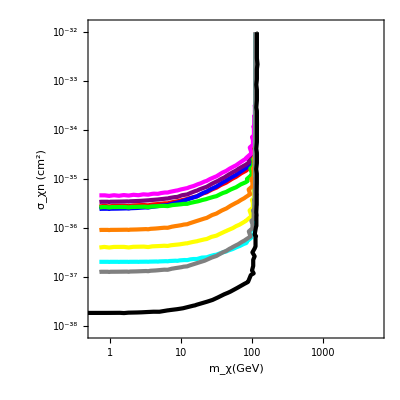

#### Plots from equilibrium age:

```mathematica
Ceq1=ContourPlot[ (Γann1[mDM,σ,Mb1,Rb1,d1]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb1,d1]==E1,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Red,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq2=ContourPlot[ (Γann1[mDM,σ,Mb2,Rb2,d2]/(4Pi*d2^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb2,d2]==E2,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Blue,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq3=ContourPlot[ (Γann1[mDM,σ,Mb3,Rb3,d3]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb3,d3]==E3,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Green,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq4=ContourPlot[ (Γann1[mDM,σ,Mb4,Rb4,d4]/(4Pi*d4^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb4,d4]==E4,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Yellow,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq5=ContourPlot[ (Γann1[mDM,σ,Mb5,Rb5,d5]/(4Pi*d5^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb5,d5]==E5,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Purple,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq6=ContourPlot[ (Γann1[mDM,σ,Mb6,Rb6,d6]/(4Pi*d6^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb6,d6]==E6,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Magenta,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq7=ContourPlot[ (Γann1[mDM,σ,Mb7,Rb7,d7]/(4Pi*d7^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb7,d7]==E7,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Orange,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq8=ContourPlot[ (Γann1[mDM,σ,Mb8,Rb8,d8]/(4Pi*d8^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb8,d8]==E8,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Cyan,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];Ceq9=ContourPlot[ (Γann1[mDM,σ,Mb9,Rb9,d9]/(4Pi*d9^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb9,d9]==E9,{mDM,0.7,5000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Gray,Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

#### Plot from stacking limit:

```mathematica
Ceqjoin=ContourPlot[((((Γann1[mDM,σ,Mb9,Rb9,d9]/(4Pi*d9^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb9,d9]))+(((Γann1[mDM,σ,Mb8,Rb8,d8]/(4Pi*d8^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb8,d8]))+(((Γann1[mDM,σ,Mb7,Rb7,d7]/(4Pi*d7^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb7,d7] ))+(((Γann1[mDM,σ,Mb6,Rb6,d6]/(4Pi*d6^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb6,d6]))+(((Γann1[mDM,σ,Mb5,Rb5,d5]/(4Pi*d5^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb5,d5]))+(((Γann1[mDM,σ,Mb4,Rb4,d4]/(4Pi*d4^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb4,d4]))+(((Γann1[mDM,σ,Mb3,Rb3,d3]/(4Pi*d3^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb3,d3] ))+(((Γann1[mDM,σ,Mb2,Rb2,d2]/(4Pi*d2^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb2,d2] ))+(((Γann1[mDM,σ,Mb1,Rb1,d1]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb1,d1])))==Ecomb/9.0,{mDM,0.1,1000000},{σ,10^-38,10^-32},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Black, Dashed,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

```mathematica
Needs["PlotLegends`"]
ShowLegend[Show[Ceq1,Ceq2,Ceq3,Ceq4,Ceq5,Ceq6,Ceq7,Ceq8,Ceq9,Ceqjoin],{{{Graphics[{Red,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 1",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Blue,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 2",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Green,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 3",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Yellow,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 4",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Purple,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 5",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Magenta,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 6",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Orange,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 7",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Cyan,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 8",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Gray,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 9",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Black,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Stacked limits",TextAlignment->Left,FontColor->Black,FontSize->18]}},LegendPosition->{-0.35,0.15},LegendSize->{0.4,0.25},LegendBorderSpace->0.0,LegendShadow->None,LegendTextOffset->{-.05,0}}]
```

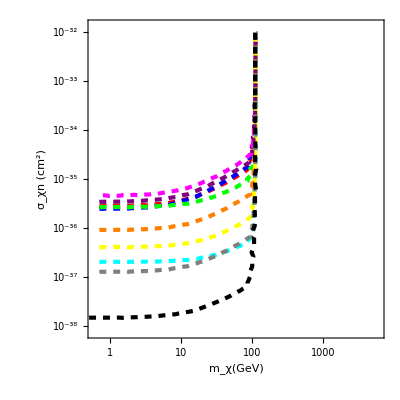

#### Comparison between the stacked limits obtained from real age and equilibrium:

```mathematica
Cjoinage11=ContourPlot[((((Γann2[mDM,σ,Mb1,Rb1,d1,Mbs1,ta1]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb1,d1]))+(((Γann2[mDM,σ,Mb2,Rb2,d2,Mbs2,ta2]/(4Pi*d2^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb2,d2]))+(((Γann2[mDM,σ,Mb3,Rb3,d3,Mbs3,ta3]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb3,d3] ))+(((Γann2[mDM,σ,Mb4,Rb4,d4,Mbs4,ta4]/(4Pi*d4^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb4,d4]))+(((Γann2[mDM,σ,Mb5,Rb5,d5,Mbs5,ta5]/(4Pi*d5^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb5,d5]))+(((Γann2[mDM,σ,Mb6,Rb6,d6,Mbs6,ta6]/(4Pi*d6^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb6,d6]))+(((Γann2[mDM,σ,Mb7,Rb7,d7,Mbs7,ta7]/(4Pi*d7^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb7,d7] ))+(((Γann2[mDM,σ,Mb8,Rb8,d8,Mbs8,ta8]/(4Pi*d8^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb8,d8] ))+(((Γann2[mDM,σ,Mb9,Rb9,d9,Mbs9,ta9]/(4Pi*d9^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb9,d9])))==Ecomb/9.0,{mDM,0.7,5000},{σ,10^-38,10^-36},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Red,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

```mathematica
Ceqjoin1=ContourPlot[((((Γann1[mDM,σ,Mb9,Rb9,d9]/(4Pi*d9^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb9,d9]))+(((Γann1[mDM,σ,Mb8,Rb8,d8]/(4Pi*d8^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb8,d8]))+(((Γann1[mDM,σ,Mb7,Rb7,d7]/(4Pi*d7^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb7,d7] ))+(((Γann1[mDM,σ,Mb6,Rb6,d6]/(4Pi*d6^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb6,d6]))+(((Γann1[mDM,σ,Mb5,Rb5,d5]/(4Pi*d5^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb5,d5]))+(((Γann1[mDM,σ,Mb4,Rb4,d4]/(4Pi*d4^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb4,d4]))+(((Γann1[mDM,σ,Mb3,Rb3,d3]/(4Pi*d3^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb3,d3] ))+(((Γann1[mDM,σ,Mb2,Rb2,d2]/(4Pi*d2^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb2,d2] ))+(((Γann1[mDM,σ,Mb1,Rb1,d1]/(4Pi*d1^2))*(mDM)^2*Ndiff[mDM]* Psurv[Rb1,d1])))==Ecomb/9.0,{mDM,0.7,5000},{σ,10^-38,10^-36},PlotRange->Full,ScalingFunctions->{"Log","Log"},ContourStyle->{Blue,AbsoluteThickness[3]},Frame->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

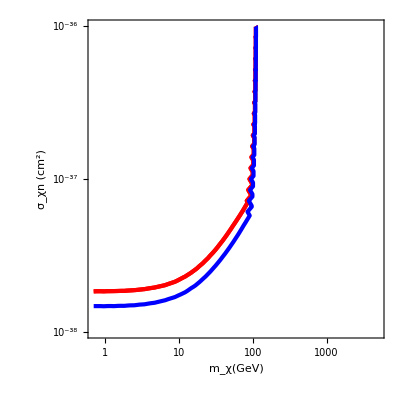

```mathematica
Show[Cjoinage11,Cjoinage1,Ceqjoin1]
```

```mathematica
Show[Cjoinage1,Ceqjoin1]
```

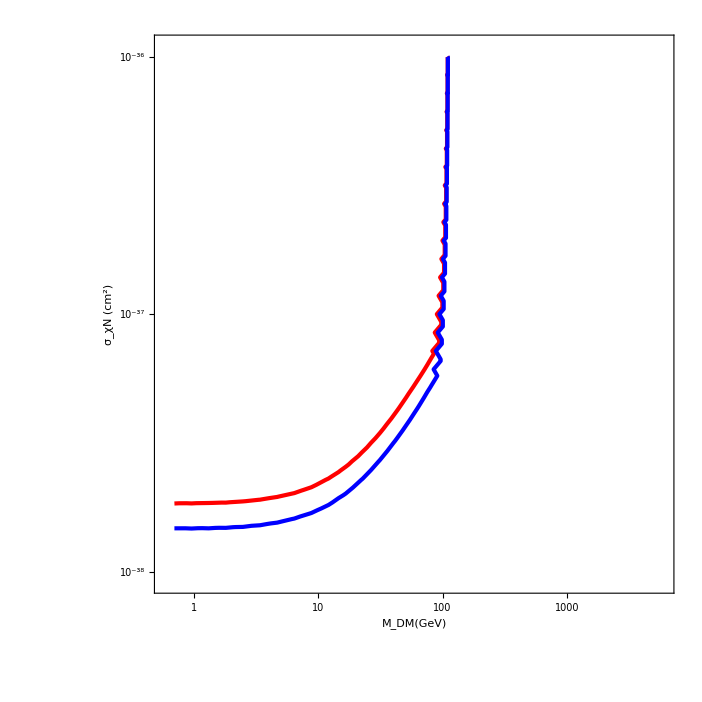

```mathematica
Needs["PlotLegends`"]
ShowLegend[Show[Cjoinage1,Ceqjoin1],{{{Graphics[{Red,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Real Age",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Blue,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Equilibrium Hp.",TextAlignment->Left,FontColor->Black,FontSize->18]}},LegendPosition->{-0.35,0.15},LegendSize->{0.4,0.25},LegendBorderSpace->0.0,LegendShadow->None,LegendTextOffset->{-.05,0}}]
```

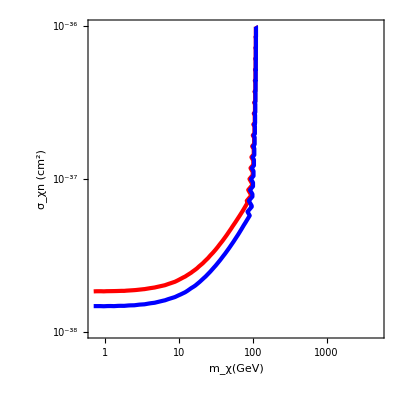

```mathematica
Needs["PlotLegends`"]
ShowLegend[Show[Ceq1,Ceq2,Ceq3,Ceq4,Ceq5,Ceq6,Ceq7,Ceq8,Ceq9],{{{Graphics[{Red,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 1",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Blue,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 2",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Green,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 3",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Yellow,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 4",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Purple,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 5",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Magenta,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 6",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Orange,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 7",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Cyan,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 8",TextAlignment->Left,FontColor->Black,FontSize->18]},{Graphics[{Gray,Dashed,AbsoluteThickness[3],Line[{Scaled[{0,0.4}],Scaled[{2.4,0.4}]}]}],Style["Source 9",TextAlignment->Left,FontColor->Black,FontSize->18]}},LegendPosition->{-0.35,0.15},LegendSize->{0.4,0.25},LegendBorderSpace->0.0,LegendShadow->None,LegendTextOffset->{-.05,0}}]
```

#### Comparison between the limits obtained from our work with other literature studies:

```mathematica
fig5=Import["/data/leane_bd.dat","Table"];
fig4=Import["/data/jupiter.dat","Table"];
fig3=Import["/data/xenon.dat","Table"];
fig2=Import["/data/pico-60.dat","Table"];
fig1=Import["/data/CDEX-SD.dat","Table"];
```

```mathematica
plot1=ListLogLogPlot[fig1,InterpolationOrder->2,PlotRange->{{0.7,10000},{10^-42,10^-31}},PlotStyle->{Red,AbsoluteThickness[3]},Frame->True,Joined->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];plot2=ListLogLogPlot[fig2,InterpolationOrder->2,PlotRange->{{0.7,10000},{10^-42,10^-31}},PlotStyle->{Blue,AbsoluteThickness[3]},Frame->True,Joined->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];plot3=ListLogLogPlot[fig3,InterpolationOrder->2,PlotRange->{{0.7,10000},{10^-42,10^-31}},PlotStyle->{Magenta,AbsoluteThickness[3]},Frame->True,Joined->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];plot4=ListLogLogPlot[fig4,InterpolationOrder->2,PlotRange->{{0.7,10000},{10^-42,10^-31}},PlotStyle->{Green,AbsoluteThickness[3]},Frame->True,Joined->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];plot5=ListLogLogPlot[fig5,InterpolationOrder->2,PlotRange->{{0.7,10000},{10^-42,10^-31}},PlotStyle->{Brown,AbsoluteThickness[3]},Frame->True,Joined->True,FrameLabel->{"m_χ(GeV)","σ_χn (cm^2)"},LabelStyle->{FontSize->24,Bold,AbsoluteThickness[3]},FrameStyle->{FontSize->24,Bold},AspectRatio->1,LabelStyle->Directive[Black,Bold,20]];
```

```mathematica
Needs["PlotLegends`"]
ShowLegend[Show[Cjoinage2,Ceqjoin2,plot1,plot2,plot3,plot4,plot5],{{{Graphics[{Black,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["Stacked limits- Real Age",TextAlignment->Left,FontColor->Black,FontSize->14]},{Graphics[{Black, Dashed,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["Stacked limits- Equilibrium Hp.",TextAlignment->Left,FontColor->Black,FontSize->14]},{Graphics[{Red,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["CDEX-10 data-Jiang et al.",TextAlignment->Left,FontColor->Black,FontSize->14]},{Graphics[{Blue,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["PICO-60 data-Amole et al.",TextAlignment->Left,FontColor->Black,FontSize->14]},{Graphics[{Magenta,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["XENON data-Aprile et al.",TextAlignment->Left,FontColor->Black,FontSize->14]},{Graphics[{Green,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["Jupiter-Leane et al.",TextAlignment->Left,FontColor->Black,FontSize->14]},{Graphics[{Brown,AbsoluteThickness[1.5],Line[{Scaled[{0,0.4}],Scaled[{1.4,0.4}]}]}],Style["GC BDs-Leane et al.",TextAlignment->Left,FontColor->Black,FontSize->14]}},LegendPosition->{-0.35,0.15},LegendSize->{0.4,0.25},LegendBorderSpace->0.1,LegendShadow->None,LegendTextOffset->{-.05,0}}]
```